# An experiment to build Turtle Geometry with basic lists and functions

## Constructor and selectors

A turtle is defined simply as a list of three things - x and y coordinates and an angle. A turtle is created by a constructor and it is accessed by some selectors.

```mathematica
MakeTurtle[x_, y_, angle_] := {x, y, angle}
```

```mathematica
TurtleX[{x_, y_, angle_}] := x
```

```mathematica
TurtleY[{x_, y_, angle_}] := y
```

```mathematica
TurtleAngle[{x_, y_, angle_}] := angle
```

## Tests of the constructor and selectors

Most part of turtle graphics can be drawn by just lines, even the arcs. So we need functions to get x, y out of a turtle and create a line.

```mathematica
TurtleLineCoords[turtles_] := {TurtleX[#], TurtleY[#]}& /@ turtles
```

Now lets test how these functions work.

```mathematica
t1 = MakeTurtle[10, 14, 30]
```

{10,14,30}

```mathematica
t2 = MakeTurtle[20, 10, 35]
```

{20,10,35}

```mathematica
{TurtleX[t2], TurtleY[t2], TurtleAngle[t2]}
```

{20,10,35}

```mathematica
{TurtleX[t1], TurtleY[t1], TurtleAngle[t1]}
```

{10,14,30}

```mathematica
TurtleLineCoords[{t1, t2}]
```

{{10,14},{20,10}}

Now lets try to draw a line between t1 and t2.

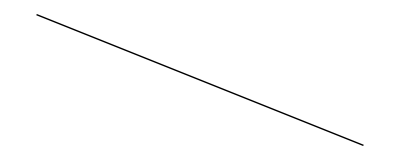

```mathematica
Graphics[Line[TurtleLineCoords[{t1, t2}]]]
```

## Drawing primitives

Now we shall define the transformation functions which will depend less on the representation of turtle and use the above functions. First the forward function.

```mathematica
TurtleFwd[turtle_, len_] := MakeTurtle[TurtleX[turtle] + Sin[TurtleAngle[turtle] Degree] * len, TurtleY[turtle] + Cos[TurtleAngle[turtle] Degree] * len, TurtleAngle[turtle]]
```

Lets test it now.

```mathematica
tf = TurtleFwd[MakeTurtle[0, 0, 0], 10]
```

{0,10,0}

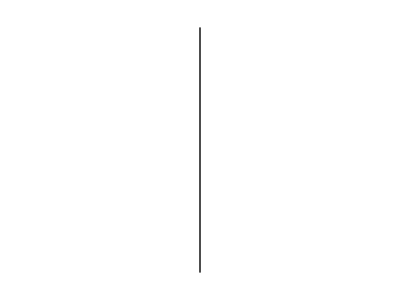

```mathematica
Graphics[Line[TurtleLineCoords[{MakeTurtle[0,0,0], TurtleFwd[MakeTurtle[0,0,0], 10]}]]]
```

Lets modify the forward function to make it a higher order function.

```mathematica
TFwd[len_] := TurtleFwd[#, len]&
```

Now we will implement the other primitives.

```mathematica
TurtleRight[turtle_, angle_] := MakeTurtle[TurtleX[turtle], TurtleY[turtle], TurtleAngle[turtle] + angle]
```

```mathematica
TRight[angle_] := TurtleRight[#, angle]&
```

```mathematica
TurtleLeft[turtle_, angle_] := MakeTurtle[TurtleX[turtle], TurtleY[turtle], TurtleAngle[turtle] - angle]
```

```mathematica
TLeft[angle_] := TurtleLeft[#, angle]&
```

## The sequencer (a.k.a. the fold)

```mathematica
TSeq[turtleFns_] := Fold[Function[{trtlist, tf}, Append[trtlist, tf[Last[trtlist]]]], #, turtleFns]&
```

With the above sequencer and the higher order functions a list of primitive modifiers can be successively applied to form turtles all the way to the last step.

```mathematica
TSeq[{TFwd[10],TRight[45], TFwd[20]}][{MakeTurtle[0,0,0]}]
```

{{0,0,0},{0,10,0},{0,10,45},{10 √2,10+10 √2,45}}

```mathematica
TurtleLineCoords[%]
```

{{0,0},{0,10},{0,10},{10 √2,10+10 √2}}

```mathematica
Line[%]
```

Line[{{0,0},{0,10},{0,10},{10 √2,10+10 √2}}]

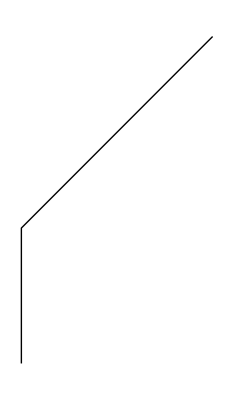

```mathematica
Graphics[%]
```

Finally, we need a convenience function to begin drawing on a list of primitives like TFwd and TRight.

## Turtle

```mathematica
Turtle[stepslist_] := Graphics[Line[TurtleLineCoords[TSeq[stepslist][{MakeTurtle[0,0,0]}]]]]
```

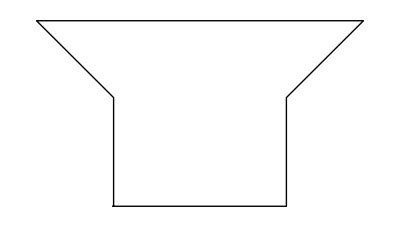

```mathematica
Turtle[{TFwd[5],TLeft[45],TFwd[5], TRight[135], TFwd[15], TRight[135], TFwd[5], TLeft[45], TFwd[5], TRight[90], TFwd[8]}]
```